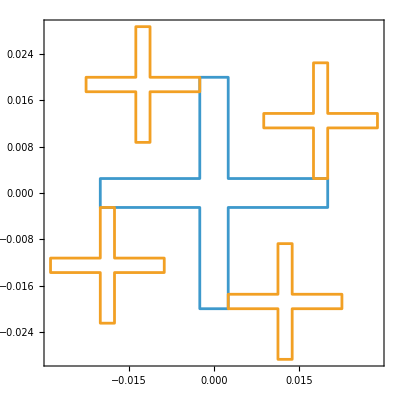

-Graphics-

```mathematica
ParamValsForPlotting={hc->0.04,wc->0.005,hw->0.02,ww->0.0025};

RegCore=Polygon[{
{wc/2,hc/2},
{-wc/2,hc/2},
{-wc/2,hc/16},
{-4wc, hc/16},
{-4wc,-hc/16},
{-wc/2,-hc/16},
{-wc/2, -hc/2},
{wc/2, -hc/2},
{wc/2, -hc/16},
{4wc, -hc/16},
{4wc,hc/16},
{wc/2,hc/16},
{wc/2, hc/2}}];

RegWing =RegionUnion[
Polygon[{
{-ww,hw},
{-4.5ww,hw},
{-4.5ww,1.4375hw},
{-5.5ww,1.4375 hw},
{-5.5ww,hw},
{-9 ww, hw},
{-9ww,0.875 hw},
{-5.5ww,0.875hw},
{-5.5ww,0.4375hw},
{-4.5ww,0.4375 hw},
{-4.5 ww,0.875 hw},
{-ww,0.875hw},
{-ww,hw}
}],
Polygon[{
{-8ww,-0.125hw},
{-8ww,-0.5625hw},
{-11.5ww,-0.5625hw},
{-11.5ww,-0.6875hw},
{-8ww, -0.6875hw},
{-8 ww, -1.125hw},
{-7ww,-1.125hw},
{-7ww,- 0.6875hw},
{-3.5 ww,-0.6875hw},
{-3.5ww,-0.5625hw},
{-7ww,-0.5625hw},
{ -7ww,-0.125 hw},
{ -8ww, -0.125hw}
}],
Polygon[{
{ww,-hw},
{4.5 ww,-hw},
{ 4.5ww,-1.4375hw},
{5.5 ww,-1.4375hw},
{5.5 ww,-hw},
{9ww,-hw},
{9 ww,-0.875 hw},
{5.5 ww,-0.875 hw},
{5.5 ww,- 0.4375hw},
{4.5 ww,-0.4375 hw},
{4.5 ww,-0.875hw},
{ww, -0.875hw},
{ww,-hw}
}],
Polygon[{
{8ww, 0.125hw},
{8 ww,0.5625hw},
{11.5 ww,0.5625hw},
{11.5 ww,0.6875hw},
{8ww,0.6875hw},
{8 ww,1.125hw},
{7 ww,1.125hw},
{7ww,0.6875hw},
{3.5 ww,0.6875hw},
{3.5 ww,0.5625hw},
{7 ww,0.5625hw},
{7 ww, 0.125hw},
{8 ww,0.125hw}}]
];

RegionPlot[{RegCore/.ParamValsForPlotting,RegWing/.ParamValsForPlotting},AspectRatio->Automatic,PlotStyle->None]
```

```mathematica
Jc2=NIntegrate[x^2+y^2,{x,y}∈RegCore/. ParamValsForPlotting]
Jw2=NIntegrate[x^2+y^2,{x,y}∈RegWing/. ParamValsForPlotting]
```

5.40625×10^-8

2.03945×10^-7

```mathematica
39.97916666666668
```

39.9792

```mathematica
Ac=NIntegrate[1,{x,y}∈RegCore/. ParamValsForPlotting]
Aw=NIntegrate[1,{x,y}∈RegWing/. ParamValsForPlotting]
```

0.000375

0.000375

```mathematica
0.000375
```

0.000375

```mathematica
Jc4=NIntegrate[(x^2+y^2)^2,{x,y}∈RegCore/. ParamValsForPlotting]
Jw4=NIntegrate[(x^2+y^2)^2,{x,y}∈RegWing/. ParamValsForPlotting]
```

1.30247×10^-11

1.2497×10^-10